```mathematica
If[!NumberQ[makePallette],NotebookEvaluate[NotebookDirectory[]~~"visualVocabDefs.nb"],NotebookEvaluate[NotebookDirectory[]~~"vvClear.nb"]];
```

## Counting by (Auto)Correlation

```mathematica
credits
```

This notebook is part of A Visual Vocabulary for Image Processing. All rights are reserved by the authors, W. A. Sethares and C. R. Johnson, Jr. Last revised Jan 2017. All x-ray images are used with permission of the Van Gogh Museum and the Rijksmuseum, Amsterdam, The Netherlands. Please do not violate the trust of the museums that have provided access to their x-ray images by distributing this data in any form.

People have highly developed visual abilities; it is easy to look at a complicated image and to make decisions about what objects are represented in the image and how many of these objects are present. When the shapes of the objects are known beforehand, they can be located via correlation. When the objects are repetitive or periodic it is possible to use autocorrelation to locate the basic period and unit of repetition. The idea that correlation can be used to find things is explored in the visual vocabulary entry for correlation. This notebook applies correlation ideas to the problem of  counting the threads in an x-ray canvas.

```mathematica
TableForm[{{Hyperlink["RotateManually",{"threadsMethodC.nb","labelRotateManually"},BaseStyle->appColor],labelRotateManually},{Hyperlink["HorizLinesCorr",{"threadsMethodC.nb","labelHorizLinesCorr"},BaseStyle->appColor],labelHorizLinesCorr},{Hyperlink["SampGauss",{"threadsMethodC.nb","labelSampGauss"},BaseStyle->appColor],labelSampGauss},{Hyperlink["CorrRowHump",{"threadsMethodC.nb","labelCorrRowHump"},BaseStyle->appColor],labelCorrRowHump},{Hyperlink["CorrPeriod",{"threadsMethodC.nb","labelCorrPeriod"},BaseStyle->appColor],labelCorrPeriod},{Hyperlink["CorrCrossProd",{"threadsMethodC.nb","labelCorrCrossProd"},BaseStyle->appColor],labelCorrCrossProd},{Hyperlink["CorrXRay",{"threadsMethodC.nb","labelCorrXRay"},BaseStyle->appColor],labelCorrXRay}}]
```

RotateManuallythreadsMethodC.nblabelRotateManuallythreadsMethodC.nbHyperlinkHyperlinkActive | An x-ray image, it's negative, and a way to rotate the image until the columns are vertical
HorizLinesCorrthreadsMethodC.nblabelHorizLinesCorrthreadsMethodC.nbHyperlinkHyperlinkActive | Looking at individual rows of the tile provides an idea of the variation in the 1D cross sections
SampGaussthreadsMethodC.nblabelSampGaussthreadsMethodC.nbHyperlinkHyperlinkActive | A sampled Gaussian shape
CorrRowHumpthreadsMethodC.nblabelCorrRowHumpthreadsMethodC.nbHyperlinkHyperlinkActive | Correlation with other humps and other rows
CorrPeriodthreadsMethodC.nblabelCorrPeriodthreadsMethodC.nbHyperlinkHyperlinkActive | Looking for the period of a row using autocorrelation
CorrCrossProdthreadsMethodC.nblabelCorrCrossProdthreadsMethodC.nbHyperlinkHyperlinkActive | Examining periodicity of the cross-product model using autocorrelation
CorrXRaythreadsMethodC.nblabelCorrXRaythreadsMethodC.nbHyperlinkHyperlinkActive | Examining periodicity of x-ray patches using autocorrelation

The central Mathematica command in this notebook is the ListCorrelate[ ] command, which functions in both one and two dimensions to carry out correlation, cross-correlation, and autocorrelation.

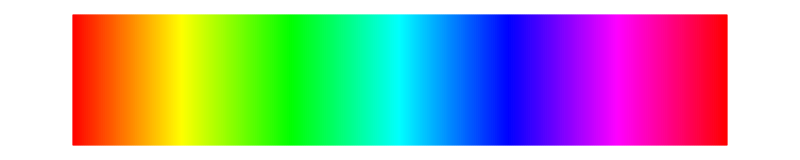

```mathematica
specLine
```

### Counting Threads in 1D

Here’s an x-ray of a small patch of a canvas from F634 showing the weave pattern and it’s negative. To make things a little easier at first, let’s straighten out the (negated) image by rotating it. Notice the extra padding around the sides. For now, we can choose the amount of rotation by eye. A value of about 0.026 radians makes the threads reasonably vertical and horizontal. You can set the value numerically by clicking the small + box and entering the desired value. If you notice that the thread counting notebooks begin the same, this is no coincidence: all four attack the same problem with different techniques.

```mathematica
labelRotateManually="An x-ray image, it's negative, and a way to rotate the image until the columns are vertical";
infoRotateManually="Choose the amount of rotation by eye.\n\nA value of about 0.026 radians makes the threads reasonably vertical and horizontal.";
Labeled[Row[{img=allImagesXray[[f634Tile]],Spacer[20],negImg=ColorNegate[img],Spacer[20],Manipulate[Show[ImageRotate[negImg,θ],ImageSize->300],Row[{Control[{{θ,0.026},-Pi/8,Pi/8,Appearance->"Labeled"}],Spacer[20],info[infoRotateManually]}],TrackedSymbols->{θ},SaveDefinitions->True]}],labelRotateManually,LabelStyle->captionStyle]
```

-Graphics--Graphics-An x-ray image, it's negative, and a way to rotate the image until the columns are vertical

```mathematica
specLine
```

-Graphics-

Consider counting along a horizontal line... which line shall we pick? With the row specified by the green line, the plot on the right shows the pixel values (normalized to lie between 0 and 1) across the image at that row. Imagine using this row of values to try and locate the threads.

```mathematica
labelHorizLinesCorr="Looking at individual rows of the tile provides an idea of the variation in the 1D cross sections";
infoHorizLinesCorr="With the row specified by the green line, the plot on the right shows the pixel values, reducing the problem to a 1D function.\n\nLook at the rows of the three models and compare with the rows of the x-ray tile. The models are much more regular.\n\nPick a row of the x-ray to work with. We'll choose row 383 to demonstrate.";
Manipulate[Module[{img,col,row},
If[invert=="negative",img=allIm[[i]],img=ColorNegate[allIm[[i]]]];
{col,row}=ImageDimensions[img];
tLine=threadLine[img,row-thisRow+1];
Row[{Show[Image[img,ImageSize->350],Graphics[{Green,Opacity[0.4],Thickness[0.02],Line[{{0,thisRow},{col,thisRow}}]}]],Spacer[20],Labeled[ListLinePlot[tLine,PlotRange->{{1,col},{0,1}},ImageSize->250],Text@"Green row displayed as a 1D function"]}]],Row[{Control[{{i,1,"image"},Thread[Range[Length[allIm]]->allImNames],ControlType->PopupMenu}],Spacer[20],Control[{{invert,"positive",""},{"negative","positive"}}]}],Row[{Control[{{thisRow,383,"row number"},1,470,1,Appearance->"Labeled"}],Spacer[40],info[infoHorizLinesFFT]}],FrameLabel->Style[labelHorizLinesFFT,Medium],TrackedSymbols->{thisRow,i,invert},SaveDefinitions->saveDef]
```

```mathematica
specLine
```

-Graphics-

In keeping with the idea of using correlation as way to find things, suppose we believe that a typical thread portrait looks something like a bell-shaped hump. Pick a convenient width for the hump:

```mathematica
labelSampGauss="A sampled Gaussian shape";
infoSampGauss="The slider controls the width of the hump.";
Manipulate[ListPlot[hump=Table[Exp[-a x^2],{x,-2,2,0.25}],Filling->Axis,PlotRange->All],Row[{Control[{{a,1.5,"width"},0.1,10,Appearance->"Labeled"}],Spacer[20],info[infoSampGauss]}],FrameLabel->Style[labelSampGauss,Medium],TrackedSymbols->{a},SaveDefinitions->True]
```

A width of about 1.5 looks plausible, for which the values of the hump are

```mathematica
hump
```

{0.00247875,0.0101149,0.0342181,0.0959671,0.22313,0.430095,0.687289,0.91051,1.,0.91051,0.687289,0.430095,0.22313,0.0959671,0.0342181,0.0101149,0.00247875}

Now correlate the hump with a row of the canvas.

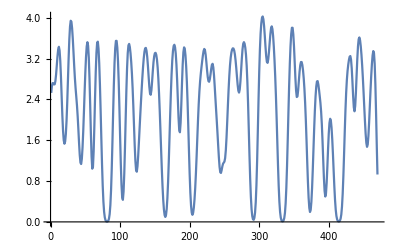
-Graphics-Correlation of the hump with a row of the canvas

```mathematica
Labeled[ListLinePlot[ListCorrelate[hump,threadLine[allIm[[1]],104]]],"Correlation of the hump with a row of the canvas",LabelStyle->captionStyle]
```

```mathematica
specLine
```

-Graphics-

Maybe we just picked a bad value for the shape... or a bad row to analyze...

```mathematica
labelCorrRowHump="Correlation with other humps and other rows";
infoCorrRowHump="Choose an image (upper left), a row of that image (upper right), and a width for the hump (lower left). The correlation between the hump and the row is plotted in the lower right.\n\nTry different widths.\n\nNo matter what width you choose (and more generally, no matter what shape you choose), all you get is a smoothed version of the thread.\n\nIt is not really going to be possible to definitively count the threads by correlating with a single preassigned shape.\n\nExplanation: consider the relationship between correlation and linear filtering; all this is doing is lowpass filtering the row.";
Manipulate[Module[{hump,col,tLine,img},
If[invert=="negative",img=allIm[[i]],img=ColorNegate[allIm[[i]]]];
hump=Table[Exp[-a x^2],{x,-2,2,0.25}];
{col,row}=ImageDimensions[img];
tLine=threadLine[img,row-thisRow+1];
GraphicsGrid[{{Show[Image[img,ImageSize->250],Graphics[{Green,Opacity[0.4],Thickness[0.02],Line[{{0,thisRow},{col,thisRow}}]}]],ListLinePlot[tLine,PlotRange->{{1,col},{0,1}},ImageSize->250]},{ListPlot[hump,Filling->Axis,PlotRange->All],ListLinePlot[ListCorrelate[hump,tLine]]}}]],Row[{Control[{{i,2,"image"},Thread[Range[Length[allIm]]->allImNames],ControlType->PopupMenu}],Spacer[20],
Control[{{invert,"negative",""},{"negative","positive"}}],Spacer[20],info[infoCorrRowHump]}],{{thisRow,383,"row number"},1,row-1,1,Appearance->"Labeled"},{{a,1.5,"hump width"},0.1,20,Appearance->"Labeled"},{row,400,ControlType->None},
FrameLabel->Style[labelCorrRowHump,Medium],TrackedSymbols->{thisRow,a,i,invert},SaveDefinitions->True]
```

It’s pretty hard to convince ourselves that this is going to be fruitful. No matter what width we choose (and more generally, no matter what shape we choose), all we get is a smoothed version of the thread. This has all the same problems encountered in the thresholding method of counting: it’s not really going to be possible to definitively count the threads. By correlating with a single preassigned shape.

HW: Pick a shape that is derived from the threadLine itself, and repeat the above experiments. Does this do any better locating the bulk of the thread crossings?

```mathematica
specLine
```

-Graphics-

But maybe there is a better way: instead of trying to guess what the shape of the hump is, why not use the actual humps? This suggests the use of autocorrelation, taking the correlation between the signal (in this case the row of the canvas) and itself. Here is the thread image and a simple way to scan through the rows, which are shown in the top right. The bottom shows the autocorrelation of this row on the left, and a zoomed in version covering the first 50 coefficients. Observe that for this image, there are (almost always) peaks in the autocorrelation at around 44 and around 22 (depending on the row chosen). These numbers represent the number of pixels the row must be shifted to achieve a maximum correlation (ignoring the peak at index “1” which represents the correlation of the signal with itself shifted zero terms). Accordingly, this suggests that a good value for the width of a thread is about 21 pixels (subtract one because the index “1” is actually a shift of zero pixels, i..e, no shift).

```mathematica
labelCorrPeriod="Looking for the period of a row using autocorrelation";
infoCorrPeriod="A better way: instead of trying to guess what the shape of the hump is, use the actual humps, i.e., the autocorrelation between the signal (in this case the row of the canvas) and itself. \n\nChoose the image (top left) and use the slider to choose a row (top right). The bottom shows the autocorrelation of this row on the left, and a zoomed in version covering the first 50 coefficients on the right. \n\nFor the x-ray tile there are often peaks in the autocorrelation at around 44 and around 22 (depending on the row chosen).\n\nThis is the number of pixels the row must be shifted to achieve a maximum correlation.\n\nAccordingly, this suggests that a good value for the width of a thread is about 21 pixels (subtract one because the index '1' is actually a shift of zero pixels, i..e, no shift).";
Manipulate[Module[{col,img,tLine,threadCorr},
If[invert=="negative",img=allIm[[i]],img=ColorNegate[allIm[[i]]]];
{col,row}=ImageDimensions[img];
tLine=threadLine[img,row-thisRow+1];
threadCorr=ListCorrelate[tLine,tLine,1];
GraphicsGrid[{{Show[Image[img,ImageSize->250],Graphics[{Green,Opacity[0.4],Thickness[0.02],Line[{{0,thisRow},{col,thisRow}}]}]],ListLinePlot[tLine,PlotRange->{{1,col},{0,1}},ImageSize->250]},{ListLinePlot[threadCorr],ListPlot[threadCorr[[1;;50]],Filling->Axis]}}]],Row[{Control[{{i,2,"image"},Thread[Range[Length[allIm]]->allImNames],ControlType->PopupMenu}],Spacer[20],
Control[{{invert,"negative",""},{"negative","positive"}}]}],Row[{Control[{{thisRow,383,"row number"},1,row-1,1,Appearance->"Labeled"}],Spacer[20],info[infoCorrPeriod]}],{row,400,ControlType->None},
FrameLabel->Style[labelCorrPeriod,Medium],TrackedSymbols->{thisRow,i,invert},SaveDefinitions->True]
```

HW: Translate this pixels per thread calculation to the inverse units of threads per cm (the image is 600 pixels per inch).

HW: Examine the columns of the thread image and estimate the average width of the threads in the columns. Translate this pixels per thread calculation to threads per cm.

HW: We manually rotated this image. Try doing the above counting by thresholding procedure on the unrotated image. Does your answer change significantly?

HW: Apply this method to other canvas patches from the thread library. Compare your answers to your earlier manual counts.

HW: Another strategy for improving the estimation would be a voting strategy:
(1) calculate the autocorrelation of every row, 
(2) record the location of the first peak for each row: this location is the “winner” 
(3) whichever location has the most winners (over all rows of the image) is the most common peak location, and the final estimate of the average thread width.

HW: Generalize the previous voting strategy to allow multiple (three) winners in each row. The global winner would again be the pixel width that occurs the most often among all the winners of all the rows. Can you think of situations where this might improve over the direct voting strategy? Can you think of situations where it might do worse?

HW: Apply the autocorrelation method to the alternating model. (a) How much noise can you add before it fails to give the expected answer. (b) Explain what happens as the slope parameter is changed. (c) Explain what happens as the relative height parameter is changed. (d) Explain what happens when the widths of the two peaks have different sizes.

HW: Make a model that replaces the slope parameter with a low frequency sinusoid (approximately 1/3 period over the window), and answer questions (a)-(d) above for this model (replace the slope parameter with the frequency of the sinusoid).

HW: make a model that changes the detailed shape of the peaks: use Sin^n for n=1/5, 1/4, 1/3, 1/2, 1, 2, 3, 4, 5. Pick a nonlinear function that has a different parametric shape (i.e., Exp, Log, etc) and use this to define the shapes of the peaks, and answer questions (a)-(d) above for these models.

HW: Apply the autocorrelation method to the random-width model. When the max and min widths are the same, this works great. Examine how the behavior worsens as the widths become less uniform.

```mathematica
specLine
```

-Graphics-

More generally, consider counting across any single line. There is a problem with this: counting (or correlating or transforming) along a line is fundamentally a one-dimensional activity, yet the “real” problem is fundamentally a two-dimensional activity. The horizontal count and the vertical count are not really independent, since crossings of one are revealed by looking at areas of the weave. For example, when counting by eye, there may be a dropout in the weave across the line we are looking at. Nonetheless, we can easily scan up and down at that point and realize that indeed there must be a thread crossing where looking at the single thread there would appear to be none.

### Counting Threads in 2D

It is clearly worth attempting to use (at least) local information around the thread on which the counting procedure is centered. The next simulation explores autocorrelation in two dimensions for cross-product models.

```mathematica
labelCorrCrossProd="Examining periodicity of the cross-product model using autocorrelation";
infoCorrCrossProd="2D autocorrelation using the cross-product model: \n\nAdjust both the vertical and horizontal frequencies in the model; the image is shown on the left and the autocorrelation is shown in the center. The right picture zooms in to the autocorrelation so it is easier to see the basic periodicities. \n\nFor the default frequencies 8 and 10, the autocorrelation shows the first peaks at 27 in the horizontal direction and 33 in the vertical. \n\nSince there are 256 pixels, a frequency of 8 is 32 pixels per repetition and the frequency 10 is 25.6 pixels per repetition. \n\nExplain why these are 1 off. \n\nObserve that the results are quite robust to additive noise. \n\nChange the frequencies and verify that the first peak in the autocorrelation tracks the period well.";
Manipulate[Module[{s,r,x,xCorr},
r=Table[Sin[2 Pi f1 t],{t,0,1,1/255}];
s=Table[Sin[2 Pi f2 t],{t,0,1,1/255}];
x=Outer[func,r,s]+n RandomReal[{-1,1},{256,256}];
xCorr=-ListCorrelate[x,x,1];
GraphicsRow[{Image[x],ArrayPlot[xCorr,PlotRange->{All,All,{Min[xCorr],Max[xCorr]}}],ArrayPlot[xCorr,PlotRange->{{1,zoom},{1,zoom},{Min[xCorr],Max[xCorr]}},FrameTicks->Automatic]},ImageSize->800]],{{f1,8,"vertical frequency"},1,30,Appearance->"Labeled"},{{f2,10,"horizontal frequency"},1,30,Appearance->"Labeled"},{{n,0.001,"noise"},0.001,5},{{zoom,50},10,200,10},Row[{Control[{{func,Plus,"combining function"},{Plus->"Plus",Times->"Times",Max->"Max",(#1^2+#2^2)&->"Norm",Clip[#1^2+#2^2,{0,1}]&->"Clipped Norm"},ControlType->SetterBar}],Spacer[20],info[infoCorrCrossProd]}],
FrameLabel->Style[labelCorrCrossProd"Examining periodicity of the cross-product model using autocorrelation",Medium],TrackedSymbols->{f1,f2,n,zoom,func},SaveDefinitions->True]
```

To understand the output, observe that for the “Plus” model with a vertical frequency of 12 oscillations per 256 points corresponds to a period of 256/12=21.6 pixels per period, which is indeed the location of the first peak in the vertical direction.  (xCorr is defined to be negative the correlation because ArrayPlot displays 1 as black and zero as white, displaying minus this effectively reverses the colormap).

HW: Explain the vertical and horizontal maxima in the autocorrelation in terms of the vertical and horizontal frequency parameters for each of the models.

```mathematica
specLine
```

-Graphics-

Applying the autocorrelation method to a variety of weave images suggests that it may be feasible to use this as an automated way to estimate the period of the weave.

```mathematica
labelCorrXRay="Examining periodicity of x-ray patches using autocorrelation";
infoCorrXRay="The image (left), the autocorrrelation (middle), and a zoom into the autocorrelation (right). \n\nThe period (in pixels) in the horizontal direction is given by the location of the first peak in the autocorrelation along the top edge of the image. \n\nThe period (in pixels) in the vertical direction is given by the location of the first peak in the autocorrelation along the left edge of the image. \n\nComment on the feasibility if using this as an automated way to estimate the period of the weave.\n\nWhy does the positive/negative button appear to leave the autocorrelation unchanged?";
Manipulate[Module[{img,imgData,imgCorr,imgCorrSmall},
If[invert=="negative",img=allImagesXray[[i]],img=ColorNegate[allImagesXray[[i]]]];
imgData=ImageData[img];
imgCorr=-ListCorrelate[imgData,imgData,1];
imgCorrSmall=imgCorr[[1;;zoom,1;;zoom]];
GraphicsRow[{img,ArrayPlot[imgCorr,PlotRange->{All,All,{Min[imgCorr],Max[imgCorr]}}],ArrayPlot[imgCorrSmall,PlotRange->{{1,zoom},{1,zoom},{Min[imgCorrSmall],Max[imgCorrSmall]}},FrameTicks->Automatic]},ImageSize->800]],Row[{Control[{{i,f634Tile,"image"},Thread[Range[numFilesX]->imageNamesX],ControlType->PopupMenu}],Spacer[20],Control[{{invert,"negative",""},{"negative","positive"}}],Spacer[20],Control[{{zoom,50},10,200,10}],Spacer[20],info[infoCorrXRay]}],FrameLabel->Style[labelCorrXRay,Medium],TrackedSymbols->{i,zoom,invert},SaveDefinitions->saveDef]
```

HW: Replace the test image with a variety of other thread images, and design a method to use the autocorrelation as a way to estimate the thread count. This will be a method that inputs the autocorrelation and then returns a numerical estimation of the horizontal and the vertical thread counts. Compare your counts to the manual counts on a number of different examples. In what situations (on which images) does your method work well? In what situations does your method give poor answers?

HW: Observe that the horizontal and vertical threads are not orthogonal to each other in all cases. Make a simple 2D sinusoidal model where the vertical and horizontal threads lie at an angle θ (not necessarily 90°). In such a case, examine how the autocorrelation function behaves.